# Computing and Plotting Wavelet Packet Transforms

One-Dimensional Wavelet Packet Transformationspaclet:WaveletWare/tutorial/Computing and Plotting Wavelet Packet Transforms#4659334 | Wavelet Packet Transforms of Matricespaclet:WaveletWare/tutorial/Computing and Plotting Wavelet Packet Transforms#902595934
Cost Functionspaclet:WaveletWare/tutorial/Computing and Plotting Wavelet Packet Transforms#314759074 | Wavelet Packet Transforms and Colorpaclet:WaveletWare/tutorial/Computing and Plotting Wavelet Packet Transforms#35148191

The WaveletWare package contains several routines for computing and visualizing wavelet packet transformations.  This tutorial describes how to use these routines.  Some of the options for computing and visualizing packet transforms are not covered here but additional information can be found on particular function help pages.

1-D Packet Transforms | Cost Functions | Packet Transforms of Matrices | Packet Transforms and Color

The two main routines in the WaveletWare package for computing wavelet packet transformations are WPTpaclet:WaveletWare/ref/WPT and WPTFullpaclet:WaveletWare/ref/WPTFull.  WPTpaclet:WaveletWare/ref/WPT takes as input either a vector, a matrix or a list of three matrices each of the same dimension and an orthogonal filter or biorthogonal filter pair and returns the resulting packet transform and best basis tree.  WPTFullpaclet:WaveletWare/ref/WPTFull takes the same input as WPT but returns the full decomposition of the input at each of a prescribed number of iterations.  The inverse wavelet packet transformation can be computed using InverseWPTpaclet:WaveletWare/ref/InverseWPT.  The FBIPacketTransformpaclet:WaveletWare/ref/FBIPacketTransform and InverseFBIPacketTransformpaclet:WaveletWare/ref/InverseFBIPacketTransform routines are special instances of the wavelet packet transform and its inverse and uses the CDF97paclet:WaveletWare/ref/CDF97 filter and a fixed best basis tree.

WPT[data,filter,opts] | Compute the wavelet packet transform
WPTFull[data,filter,opts] | Full decomposition at several levels of the packet transform
InverseWPT[data,filter,opts] | Compute the inverse wavelet packet transform
FBIPacketTransform[data,opts] | Wavelet packet transform with fixed tree and filter
InverseFBIPacketTransform[data,opts] | Inverse wavelet packet transform with fixed tree and filter

Wavelet packet transform functions.

Any of the following filters can be used with WPTpaclet:WaveletWare/ref/WPT, WPTFullpaclet:WaveletWare/ref/WPTFull or InverseWPTpaclet:WaveletWare/ref/InverseWPT:

Coif[n,opts] | Coiflet filter of length 6n, n=1,2,3,4,5
CDF97[] | Cohen/Daubechies/Feauveau biorthogonal filter pair
Daub[n,opts] | Daubechies filter of even length n
Haar[] | Haar filter
LeGall[] | LeGall biorthogonal filter pair
SplineFilters[n,m,opts] | Biorthogonal spline filter pair

Orthogonal and biorthogonal filters.

The WaveletWare package contains a variety of routines that can be used for visualizing wavelet packet transforms.

WaveletVectorPlot[data,tree,opts] | Plot the wavelet packet transform of 1-d data
FullWaveletVectorPlot[data,opts] | Plot all iterations of wavelet packet transforms of 1-d data
WaveletPlot[data,tree,opts] | Plots the wavelet packet transform of a matrix or 3 matrices
FullWaveletPlot[data,opts] | Plots all iterations of a wavelet packet transform of input data
WaveletRegionPlot[data,region,opts] | Plots particular regions of a wavelet packet transform
ShowBestBasis[tree,opts] | Graphical description (2- and 3-d) of the best basis tree

Routines to visualize wavelet packet transforms.

This loads the package:

```mathematica
<<WaveletWare`
```

## One-Dimensional Wavelet Packet Transformations

(top)

Given a number of iterations n, a vector v whose length is divisible by 2^n, and an orthogonal filter (or biorthogonal filter pair),  the wavelet packet transform first computes the wavelet transform of v (see the tutorial Computing and Plotting Wavelet Transformations).  The wavelet transform is then iteratively applied to each low- and high-pass portion of the previous computation.  The result is a list of n+1 vectors (counting the original vector v).   The process is demonstrated below.

```mathematica
g[t_]:=Sqrt[t(1-t)]*Sin[2Pi (1.05)/(t+.05)];
n=1024;
v=g[Range[0,1-1/n,1/n]];

wptfull=WPTFull[v,Haar[],NumIterations->3];
FullWaveletVectorPlot[wptfull,PacketPlot->True] // TableForm
```

-Graphics-

The graph below illustrates the procedure.

```mathematica
ShowBestBasis[{1,{0,0},{0,0,0,0},{0,0,0,0,0,0,0,0}},ColorOn->Lighter[Gray],ColorOff->Lighter[Gray]]
```

-Graphics-

## Cost Functions

(top)

Once the full decomposition is computed, the last step in computing the packet transform is to determine the "best basis" for the decomposition.  Some best basis options are plotted below.  Note that the last basis is the standard wavelet decomposition.  More information on the tree structure in the WaveletWare package can be found in the tutorial Data Structures in the WaveletWare Package.

```mathematica
trees={{0,{1,1},{0,0,0,0},{0,0,0,0,0,0,0,0}},{0,{0,0},{1,0,0,1},{0,0,1,1,1,1,0,0}},{0,{0,0},{0,0,0,1},{1,1,1,1,1,1,0,0}},WaveletTree[3]};
Map[ShowBestBasis,trees] // TableForm
```

-Graphics-

To determine the best basis, the packet transformation uses a cost function.  A cost function Cpaclet:ref/C maps the 0 vector to 0 and for any partition of input vector v = [ u | w ], Cpaclet:ref/C(v) = Cpaclet:ref/C(u)+Cpaclet:ref/C(w).  The best basis algorithm starts at the bottom of the packet decomposition and compares the sum of the cost of two "children" with the cost of its "parent."  The data representing the lower cost is retained for continued comparison.  The process ends by comparing costs computed to date with the cost of the original data.

The WaveletWare package has four built-in cost functions.  They are listed below.

NumberAboveThreshold[data,t] | Number of values (in absolute) ≥ t
NumberNonzero[data] | Number of nonzero values in data
ShannonEntropy[data] | Shannon Entropy of data
SumOfPowers[data,p] | Sum of the values in data (in absolute) raised to power p

Cost functions in the WaveletWare package.

The WaveletWare function BestBasisTreepaclet:WaveletWare/ref/BestBasisTree will compute the best basis given the full decomposition.  The CostFunctionpaclet:WaveletWare/ref/CostFunction option can be set to something other than the default function NumberNonzeropaclet:WaveletWare/ref/NumberNonzero.  In the cases where the cost function has a second argument (such as NumberAboveThresholdpaclet:WaveletWare/ref/NumberAboveThreshold or SumOfPowerspaclet:WaveletWare/ref/SumOfPowers), the option SecondParameterpaclet:WaveletWare/ref/SecondParameter should be set.  A simple example is given below.

```mathematica
v=Range[16];
wt=Chop[WPTFull[v,Haar[],NumIterations->3]];
tree1=BestBasisTree[wt];
tree2=BestBasisTree[wt,CostFunction->NumberAboveThreshold,SecondParameter->5];
Map[ShowBestBasis,{tree1,tree2}] // TableForm
```

-Graphics-

Returning to the original example where the input is samples of the Donoho/Johnstone Doppler function, the computations below compute the wavelet packet transform using the biorthogonal (5,3) spline filter pair.  We use the cost function NumberAboveThresholdpaclet:WaveletWare/ref/NumberAboveThreshold instead of the default NumberNonzeropaclet:WaveletWare/ref/NumberNonzero.  The best basis tree is plotted.  In order to plot the transformed data, the optional tree argument must be passed to WaveletVectorPlotpaclet:WaveletWare/ref/WaveletVectorPlot.

-Graphics-

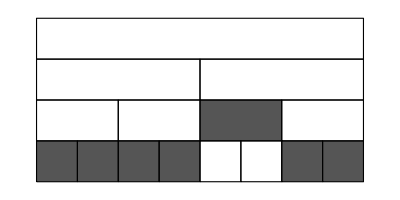

-Graphics-

```mathematica
g[t_]:=Sqrt[t(1-t)]*Sin[2Pi (1.05)/(t+.05)];
n=1024;
v=g[Range[0,1-1/n,1/n]];
ListPlot[v,Ticks->{Range[0,n,n/4],Range[-1/2,1/2]},PlotLabel->"Data Samples"]

{wt,tree}=WPT[v,SplineFilters[2,2],NumIterations->3,CostFunction->NumberAboveThreshold,SecondParameter->.1];
ShowBestBasis[tree]
WaveletVectorPlot[wt,tree,NumIterations->3]
```

The Iterationpaclet:WaveletWare/ref/Iteration parameter can be used to plot only particular regions of the packet transform.  One example is given here.  See help for WaveletPlotpaclet:WaveletWare/ref/WaveletPlot or Iterationpaclet:WaveletWare/ref/Iteration for more information.

```mathematica
WaveletVectorPlot[wt,tree,Iteration->{{3,1},{3,2},{2,3}},ImageSize->400]
```

-Graphics-

The inverse packet transform can be computed using InverseWPTpaclet:WaveletWare/ref/InverseWPT.

```mathematica
inv=InverseWPT[{wt,tree},SplineFilters[2,2]];
ListPlot[inv,Ticks->{Range[0,n,n/4],Range[-1/2,1/2]},PlotLabel->"Data Samples",ImageSize->400]
Chop[v]==Chop[inv]
```

-Graphics-

True

## Wavelet Packet Transforms of Matrices

(top)

When the input is a matrix, the packet routine WPTpaclet:WaveletWare/ref/WPT again uses WPTFullpaclet:WaveletWare/ref/WPTFull to compute full decomposition (for a prescribed number of iterations).  

An example is given below.  Note that the option PacketPlotpaclet:WaveletWare/ref/PacketPlot must be set to True so that FullWaveletPlotpaclet:WaveletWare/ref/FullWaveletPlot knows to plot a packet transform.

```mathematica
file=PackageDirectory[DataType->Images]<>"benches.png";
A=ImageRead[file,Resize->{256,384}];

wt=WPTFull[A,Daub[4],NumIterations->3];
FullWaveletPlot[wt,PacketPlot->True,ImageSize->384]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

BestBasisTreepaclet:WaveletWare/ref/BestBasisTree with the cost function NumberAboveThresholdpaclet:WaveletWare/ref/NumberAboveThreshold is used to determine a best basis for the decomposition.

```mathematica
tree=BestBasisTree[wt,CostFunction->NumberAboveThreshold,SecondParameter->10];
ShowBestBasis[tree,ImageSize->400]
```

-Graphics-

The above computations are consolidated by WPTpaclet:WaveletWare/ref/WPT and the results are plotted using WaveletPlotpaclet:WaveletWare/ref/WaveletPlot with the option argument tree included.

```mathematica
file=PackageDirectory[DataType->Images]<>"benches.png";
A=ImageRead[file,Resize->{256,384}];

{wt,tree}=WPT[A,Daub[4],NumIterations->3,CostFunction->NumberAboveThreshold,SecondParameter->10];
ShowBestBasis[tree,Show3D->False]
WaveletPlot[wt,tree,NumIterations->3]
```

-Graphics-

-Graphics-

The Iterationpaclet:WaveletWare/ref/Iteration option can be used to plot particular regions in the packet transform.  See the reference pages for WaveletPlotpaclet:WaveletWare/ref/WaveletPlot or Iterationpaclet:WaveletWare/ref/Iteration for more details.

```mathematica
file=PackageDirectory[DataType->Images]<>"benches.png";
A=ImageRead[file,Resize->{256,384}];

{wt,tree}=WPT[A,Daub[4],NumIterations->3,CostFunction->NumberAboveThreshold,SecondParameter->10];
ShowBestBasis[tree,Show3D->False]
WaveletPlot[wt,tree,NumIterations->3,Iteration->{{3,1,1},{3,1,2},{2,1,4},{1,2,2}}]
```

-Graphics-

-Graphics-

The WaveletWare function WaveletRegionPlotpaclet:WaveletWare/ref/WaveletRegionPlot can also be used to plot particular portions of a packet transform.  In this case, Iterationpaclet:WaveletWare/ref/Iteration is not an option but the third argument of this function.

```mathematica
file=PackageDirectory[DataType->Images]<>"benches.png";
A=ImageRead[file,Resize->{256,384}];

{wt,tree}=WPT[A,Daub[4],NumIterations->3,CostFunction->NumberAboveThreshold,SecondParameter->10];
ShowBestBasis[tree,Show3D->False]
WaveletRegionPlot[wt,tree,{{3,1,1},{3,1,2},{2,1,4},{1,2,2}}]

(* Use the mouse to navigate through the output of the command below *)
WaveletRegionPlot[wt,tree,{{3,1,1},{3,1,2},{2,1,4},{1,2,2}},PresentationStyle->FlipView]
```

-Graphics-

-Graphics-

## Wavelet Packet Transforms and Color

(top)

WPTpaclet:WaveletWare/ref/WPT and WPTFullpaclet:WaveletWare/ref/WPTFull can take as input lists of three matrices each of the same dimension (presumably these are channels from a color space such as RGB, YCbCr or HSI).  The output can be plotted with WaveletPlotpaclet:WaveletWare/ref/WaveletPlot.

```mathematica
file=PackageDirectory[DataType->Images]<>"waves.png";
A=ImageRead[file,Resize->{256,384}];
ImagePlot[A]
Map[ImagePlot,A] // GraphicsRow

{wt,tree}=WPT[A,Daub[4],NumIterations->3,CostFunction->NumberAboveThreshold,SecondParameter->10];
Map[ShowBestBasis[#,Show3D->False]&,tree] // GraphicsRow
WaveletPlot[wt,tree] // GraphicsRow
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

Unless the best basis structure is the same for all channels, WaveletPlotpaclet:WaveletWare/ref/WaveletPlot displays the channels separately.  Alternatively, the option CompositeTreepaclet:WaveletWare/ref/CompositeTree can be set to True in WPTpaclet:WaveletWare/ref/WPT and then a single best basis tree is used for all channels.  To plot the channels together, set the PlotTogetherpaclet:WaveletWare/ref/PlotTogether option in WaveletPlotpaclet:WaveletWare/ref/WaveletPlot to True.

```mathematica
file=PackageDirectory[DataType->Images]<>"facade.png";
A=ImageRead[file,Resize->{256,384}];
ImagePlot[A]

{wt,tree}=WPT[A,Daub[4],NumIterations->3,CostFunction->NumberAboveThreshold,SecondParameter->10,CompositeTree->True];
ShowBestBasis[tree,Show3D->False]

WaveletPlot[wt,tree] // GraphicsRow
WaveletPlot[wt,tree,PlotTogether->True]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

WaveletPlotpaclet:WaveletWare/ref/WaveletPlot can be instructed to plot particular regions of the packet transform.  In the case of color images, the Iteration option becomes a list of 4-tuples with the first value representing the channel (1,2,3), the second value the iteration and the last two values the matrix block to be plotted.  In this case when the same basis tree is used for all channels, the term All can be used for the first value of the 4-tuple and then all channels of that particular region are plotted.

```mathematica
file=PackageDirectory[DataType->Images]<>"fish.png";
A=ImageRead[file,Resize->{256,384}];
ImagePlot[A]

{wt,tree}=WPT[A,Daub[4],NumIterations->3,CostFunction->NumberAboveThreshold,SecondParameter->10];
Map[ShowBestBasis[#,Show3D->False]&,tree] // GraphicsRow

WaveletPlot[wt,tree,Iteration->{{1,1,2,1},{1,2,2,1},{2,3,5,7},{3,3,1,1}}]

WaveletPlot[wt,tree,Iteration->{{All,2,2,1}}]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

WPTFullpaclet:WaveletWare/ref/WPTFull can process color images.  The results are plotted by FullWaveletPlotpaclet:WaveletWare/ref/FullWaveletPlot with PacketPlotpaclet:WaveletWare/ref/PacketPlot set to True.

```mathematica
file=PackageDirectory[DataType->Images]<>"cups.png";
A=ImageRead[file,Resize->{256,384}];

wt=WPTFull[A,Daub[4],NumIterations->2];
FullWaveletPlot[wt,PacketPlot->True] 

FullWaveletPlot[wt,PacketPlot->True,PlotTogether->True]
```

-Graphics-

-Graphics-

Related Tutorials

Computing and Plotting Wavelet Transformations